# Galerkin Method Practice

## Examples from Computational Galerkin Methods

by C. A. J. Fletcher

Andrew Senchuk

Department of Physics and Astronomy

October 10, 2013

## Simple Examples

### 1. An ordinary differential equation

Consider the ordinary differential equation:

ⅆy[x]/ⅆx-y[x]=0

with the boundary condition y = 1 at x = 0.  An appropriate solution is sought in the domain 0 ≤ x ≤ 1 ( the exact solution is y = e^x ).  An appropriate ( trial) solution is introduced by:

```mathematica
y[x_,n_]:=1+∑_(j=1)^n a[j] x^j
```

where the leading term is included to satisfy the boundary condition.  The trial functions x^j then satisfy homogeneous boundary conditions.  Deliberately structuring the trial solution to satisfy the boundary conditions is a common practice in applying the traditional Galerkin method.  Usually this technique produces a more accurate solution for a given number of unknowns, N.  Selecting value for N first:

```mathematica
n=2;
```

Calculating the residual, R

```mathematica
R=D[(y[x,n]), x]-y[x,n]
```

{-1/7+(6 x)/7-(6 x^2)/7}

Simplifying:

```mathematica
FullSimplify[R]
```

{1/7 (-1-6 (-1+x) x)}

To apply the Galerkin method we must apply the inner product defined to be:

```mathematica
innerProduct[f_,g_,a_,b_]:=∫_a^b f gⅆx
```

```mathematica
T=Table[innerProduct[R,x^(k-1),0,1]==0,{k,1,n}]
```

{{0}==0,{0}==0}

for k = 1, ... , N.  This produces a system of equations which must now be solved.  To facilitate this, we introduce a vector of the unknown coefficients:

```mathematica
coeffs=Table[a[j],{j,1,n}]
```

{a[1],a[2]}

This system of equations can now be solved using the Solve function:

```mathematica
solved=Solve[T,coeffs]
```

{{}}

We can now construct the trial solution by substitution of the above into the trial function:

```mathematica
y[x,n]=1+∑_(j=1)^n a[j] x^j/.solved
```

{1+x a[1]+x^2 a[2]}

```mathematica
yt=Extract[%,{1}]
```

1+x a[1]+x^2 a[2]

Now we can plot the solution and compare it with the exact solution y = ⅇ^x:

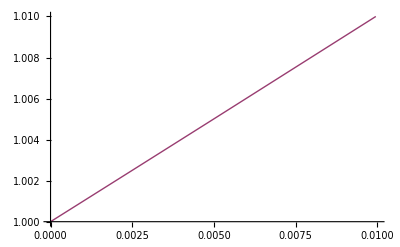

```mathematica
Plot[{yt,ⅇ^x},{x,0,1},PlotRange->{{0,.01},{0.99999,1.01}}]
```

Here is the same problem, solved using B-Polynomials instead:

{{a[1]→6/13,a[2]→22/13}}

1+12/13 (1-x) x+(22 x^2)/13

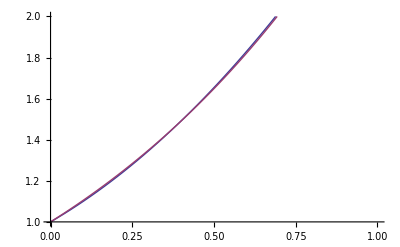

```mathematica
bPolynomial[n_,i_,a_,b_,x_]:=Binomial[n,i]((x-a)^i (b-x)^(n-i))/(b-a)^n ;
v[x_,n_]:=1+∑_(j=1)^n a[j] bPolynomial[n,j,0,1,x]
Res=D[(v[x,n]), x]-v[x,n];

A=Table[innerProduct[Res, bPolynomial[n,k-1,0,1,x],0,1]==0,{k,1,n}];
vars=Table[a[j],{j,1,n}];

coefs=Solve[A,vars]
yyt=Extract[(1+∑_(j=1)^n a[j]  bPolynomial[n,j,0,1,x]/.coefs),{1}]
Plot[{yyt,ⅇ^x},{x,0,1},PlotRange->{{0,1},{1,2}}]
```

### 2. An eigenvalue problem

Consider the model eigenvalue problem governed by:

(ⅆ^2 P[x])/(ⅆ x^2)+λP[x]=0

with the boundary condition P(0) = P(1) = 0.  An appropriate solution is sought in the domain 0 ≤ x ≤ 1 ( This problem has an exact solution.  The exact eigenvalues are given by   while the exact eigenfunctions are P_j(x) = √2 sin(jπx), j = 1, 2, 3, ... ).  An appropriate ( trial) solution is introduced by:

```mathematica
P[i_,x_]:= (x-x^(i+1))
```

where the form of the trial solutions has been chosen to satisfy the boundary conditions exactly.  The trial functions x^j then satisfy homogeneous boundary conditions.  Selecting value for N first:

```mathematica
s=2;
```

It is useful to define the differential equation in terms of operator form:

```mathematica
L[f_]:=D[f,{x,2}]+λ f
```

To apply the Galerkin method we must apply the inner product defined to be:

```mathematica
innerProduct[f_,g_,a_,b_]:=∫_a^b f gⅆx
```

Calculating the residual, R, in matrix form:

```mathematica
Lmat[i_,j_]:=innerProduct[P[i,x],L[P[j,x]],0,1]
```

And now we calculate the RHS of the Galerkin inner product

```mathematica
ρvec[i_]:=innerProduct[P[i,x],0,0,1]
```

This produces a system of equations which must now be solved.  To facilitate this,

```mathematica
eqns=Table[Sum[Lmat[i,j] c[j],{j,1,s}]==ρvec[i],{i,1,s}]
```

{(-1/3+λ/30) c[1]+(-1/2+λ/20) c[2]==0,(-1/2+λ/20) c[1]+(-4/5+(8 λ)/105) c[2]==0}

```mathematica
M1=Extract[eqns,{1}]
M2=Extract[eqns,{2}]
```

(-1/3+λ/30) c[1]+(-1/2+λ/20) c[2]==0

(-1/2+λ/20) c[1]+(-4/5+(8 λ)/105) c[2]==0

we introduce a vector of the unknown coefficients:

```mathematica
koeffs=Table[c[j],{j,1,s}]
```

{c[1],c[2]}

This system of equations can now be solved using the Solve function to obtain λ:

```mathematica
R=Table[(Lmat[i,j]),{i,1,s},{j,1,s}]
Solve[Det[R]==0,λ]
```

{{-1/3+λ/30,-1/2+λ/20},{-1/2+λ/20,-4/5+(8 λ)/105}}

{{λ→10},{λ→42}}

To extract the coefficients, we can make use of the the fact that the solution must be orthonormalized:

```mathematica
norm=innerProduct[Pa[x,n],Pa[x,n],0,1]==1
```